# Karol Peszek - Zestaw 3

Zadanie 1.

```mathematica
f[x_] := x^4 + x^3 + x^2 + 2
```

```mathematica
roots = ComplexExpand[Solve[f[x] == 0, x]];
roots (*complex roots*)
```

{{x→-1-ⅈ},{x→-1+ⅈ},{x→1/2+(ⅈ √3)/2},{x→1/2-(ⅈ √3)/2}}

```mathematica
solutions=x/. roots;
polarpairs={Abs[#],Arg[#]}&/@ solutions (*polar pairs*)
```

{{√2,-(3 π)/4},{√2,(3 π)/4},{1,π/3},{1,-π/3}}

Zadanie 2.

```mathematica
ClearAll[roots];
z = -3 - 4 * I; (*define the complex number*)
```

```mathematica
roots=Table[Power[z,1/7] Exp[2 Pi I k/7],{k,0,6}] (*expanded roots*)
```

{(-3-4 ⅈ)^(1/7),(-3-4 ⅈ)^(1/7) ⅇ^((2 ⅈ π)/7),(-3-4 ⅈ)^(1/7) ⅇ^((4 ⅈ π)/7),(-3-4 ⅈ)^(1/7) ⅇ^((6 ⅈ π)/7),(-3-4 ⅈ)^(1/7) ⅇ^(-(6 ⅈ π)/7),(-3-4 ⅈ)^(1/7) ⅇ^(-(4 ⅈ π)/7),(-3-4 ⅈ)^(1/7) ⅇ^(-(2 ⅈ π)/7)}

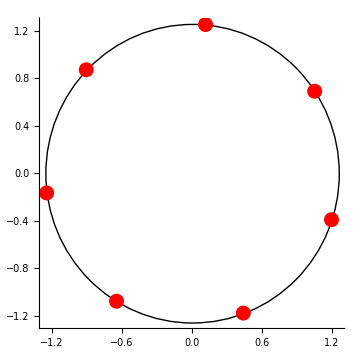

```mathematica
r=Abs[z]^(1/7); (*circle radius*)
Graphics[{Circle[{0,0},r],{Red,PointSize[0.03],Point[{Re[#],Im[#]}&/@roots]}},Axes->True,AspectRatio->1] (*draw a plot*)
```

Zadanie 3.

```mathematica
ClearAll[z];
eq=(3-I) z^2+(4+I) z+3 I==0; (*define the equation*)
```

```mathematica
sol=Solve[eq,z]
```

{{z→(3/20+ⅈ/20) ((-4-ⅈ)+√(3-28 ⅈ))},{z→(-3/20-ⅈ/20) ((4+ⅈ)+√(3-28 ⅈ))}}

```mathematica
zReIm={Re[#],Im[#]}&/@(z/. sol) (*expand the roots into real and imaginary numbers*)
```

{{1/20 (1-Im[√(3-28 ⅈ)])+3/20 (-4+Re[√(3-28 ⅈ)]),3/20 (-1+Im[√(3-28 ⅈ)])+1/20 (-4+Re[√(3-28 ⅈ)])},{1/20 (1+Im[√(3-28 ⅈ)])-3/20 (4+Re[√(3-28 ⅈ)]),-3/20 (1+Im[√(3-28 ⅈ)])+1/20 (-4-Re[√(3-28 ⅈ)])}}

Zadanie 4.

```mathematica
ClearAll["Global`*"]
(*define the triangle*)
a={-1,-1,0};
b={3,1,0};
c={2,6,0};
(*define the triangle*)
triangle={a,b,c,a};
```

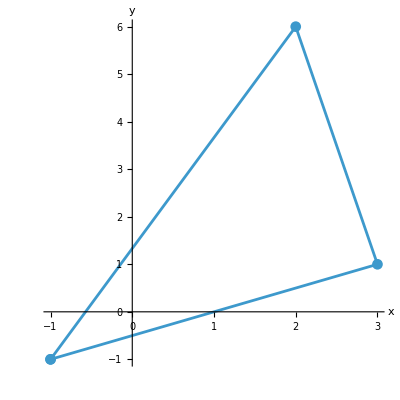

```mathematica
(*draw the triangle on a plane*)
ListLinePlot[triangle[[All,{1,2}]],AxesLabel->{"x","y"},PlotMarkers->Automatic,PlotRange->All,AspectRatio->1]
```

```mathematica
(*calculate lengths of the sides*)
ab=Norm[b-a]
bc=Norm[c-b]
ca=Norm[a-c]
```

2 √5

√26

√58

```mathematica
(*calculate the area of the triangle*)
area=1/2 Norm[Cross[b-a,c-a]]
```

11

```mathematica
(*rotate the triangle by 30 degrees arroung the z axis*)
theta=Pi/6; (*30 stopni*)
rotationMatrix={{Cos[theta],-Sin[theta],0},{Sin[theta],Cos[theta],0},{0,0,1}};

aprime=rotationMatrix.a;
bprime=rotationMatrix.b;
cprime=rotationMatrix.c;
trianglePrime={aprime,bprime,cprime,aprime};
```

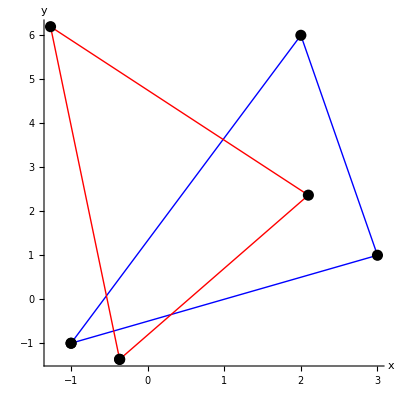

```mathematica
(*draw the rotated triangle in relation to the original one*)
Graphics[{{Blue,Thick,Line[triangle[[All,{1,2}]]]},{Red,Thick,Line[trianglePrime[[All,{1,2}]]]},{Black,PointSize[0.02],Point[triangle[[All,{1,2}]]]},{Black,PointSize[0.02],Point[trianglePrime[[All,{1,2}]]]}},Axes->True,AxesLabel->{"x","y"},AspectRatio->1]
```

Zadanie 5.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*define points*)
F1={-2,5};
F2={3,2};
```

```mathematica
(*define the medium point*)
M=(F1+F2)/2;
```

```mathematica
symetralna[x_]:=((F2[[1]]-F1[[1]])/(F1[[2]]-F2[[2]]))*(x-M[[1]])+M[[2]];
```

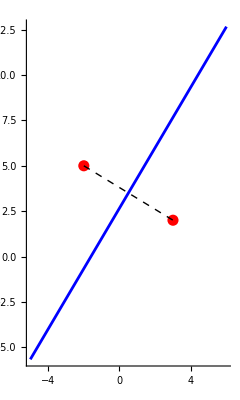

```mathematica
(*plot on a graph*)
Show[Graphics[{Red,PointSize[0.02],Point[F1],Point[F2]}],Plot[symetralna[x],{x,-5,6},PlotStyle->Blue],Graphics[{Dashed,Line[{F1,F2}]}],Axes->True]
```

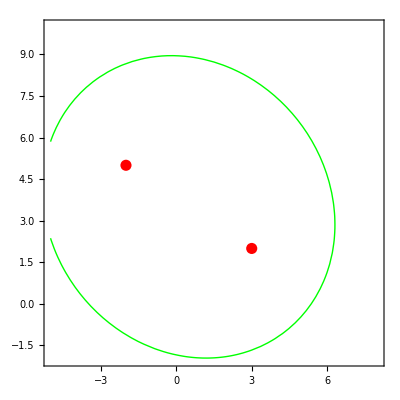

```mathematica
(*plot the elypsis*)
elipsa=ContourPlot[Sqrt[(x+2)^2+(y-5)^2]+Sqrt[(x-3)^2+(y-2)^2]==12,{x,-5,8},{y,-2,10},ContourStyle->{Thick,Green}];

Show[elipsa,Graphics[{Red,PointSize[0.02],Point[F1],Point[F2]}],Axes->True]
```

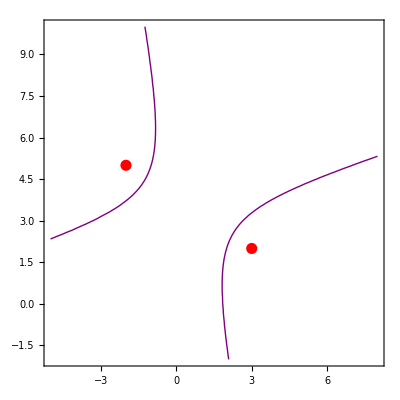

```mathematica
(*draw hyperbola*)
hiperbola=ContourPlot[Abs[Sqrt[(x+2)^2+(y-5)^2]-Sqrt[(x-3)^2+(y-2)^2]]==4,{x,-5,8},{y,-2,10},ContourStyle->{Thick,Purple}];

Show[hiperbola,Graphics[{Red,PointSize[0.02],Point[F1],Point[F2]}],Axes->True]
```